```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0;
```

```mathematica
SetAttributes[{a,b,c,α,β},Constant];
```

```mathematica
f0[t_]:=α+β t
```

```mathematica
f1[t_]:=α
```

```mathematica
g0[x_]:=α
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→α-t (-1+x) β+-(2 (1-ⅇ^(-π^2 t 𝒟 K[1]^2)) β Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞}}

```mathematica
Yf[x_,t_,a_,b_,d_]:=a+t(1-x)b+∑_(k=1)^100 (2(ⅇ^(-π^2 t d k^2)-1)b Sin[π x k])/(π^3 k^3)
```

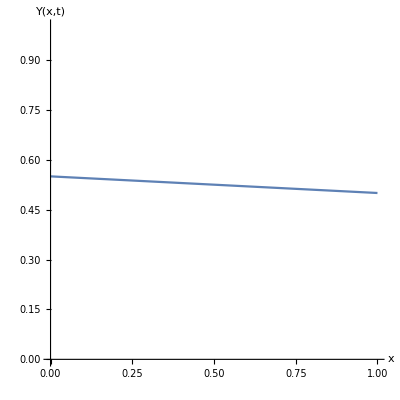

```mathematica
Plot[{Yf[x,0.5,0.5,0.1,0.0001]},{x,0,1},PlotRange->{0,1},AxesLabel->{"x","Y(x,t)"},PlotLegends->Automatic,AspectRatio->1]
```